```mathematica
ClearAll["Global`*"];
Ufazor=12.+7 ⅉ;
Amp=Abs[Ufazor]
ϕ=Arg[Ufazor]
```

13.8924

0.528074

```mathematica
ClearAll["Global`*"];
Amp=15;
ϕ=π/3;
Ufazor=Amp*ⅇ^(ⅈ*ϕ);
N[Ufazor]
```

7.5+12.9904 ⅈ

```mathematica
ClearAll["Global`*"];
9.2*ⅇ^(ⅉ*2.4)
```

-6.78402+6.21426 ⅈ

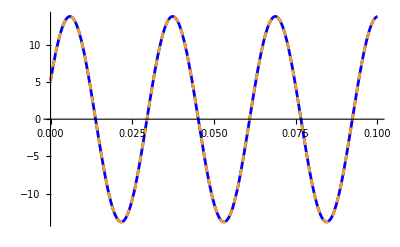

```mathematica
ClearAll["Global`*"];
Ufazor=12.8+5.2ⅉ;ω=200;
Plot[{Abs[Ufazor]*Sin[ω*t+Arg[Ufazor]], Im[Ufazor*ⅇ^(ⅉ*ω*t)]},{t,0,100*10^-3},PlotStyle->{Blue,Dashed}]
```

{{Iz→0.000952885-0.00340498 ⅈ,Ir→0.00283748+0.000794071 ⅈ,Ic→-0.000952885+0.00340498 ⅈ,Il→0.0018846+0.00419905 ⅈ,U1→3.3+1. ⅈ,U2→3.40498+0.952885 ⅈ}}

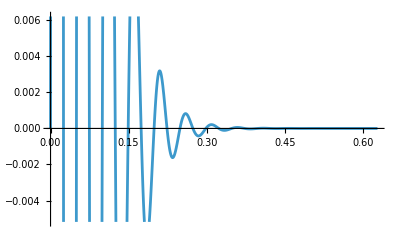

```mathematica
ClearAll["Global`*"];
(*HUS*)
(* 
Uz[t]->Ufazor,
[t] -> " ",
il[0]==0 -> " ",
' -> ⅉ*ω,
*)

(*u[t]=12.5*Sin[105t+1.2] -> 12.5*ee^(jj*1.2)*)
suciastky={R->1.2 *10^3,C1->10*10^-6,L->250*10^-3,Uz->3.3+ⅉ,ω->100};

rovnice={

0==Iz+Ic,
Il==Ic+Ir,

U2==R*Ir,
U1-U2==L*Il*ⅉ*ω,
Ic==C1*U2*ⅉ*ω,
Uz==U1
};

nezname={Iz,Ir,Ic,Il,U1,U2};
riesenie=Solve[rovnice/.suciastky,nezname]
Plot[Im[U2^(ⅉ*ω*t)]/.suciastky/.riesenie,{t,0,10*2*π/ω/.suciastky}]
```

{Iz→-((3/5000+(3 ⅈ)/2500) (-25 ⅈ+π) (-5000 ⅈ+π))/(-250000-5100 ⅈ π+3 π^2),Ir1→((3/5000+(3 ⅈ)/2500) (-25 ⅈ π+π^2))/(-250000-5100 ⅈ π+3 π^2),Ir2→((3/10000+(3 ⅈ)/5000) π (-5000 ⅈ+π))/(-250000-5100 ⅈ π+3 π^2),Ir3→((3/10000+(3 ⅈ)/5000) (-250000-5050 ⅈ π+π^2))/(-250000-5100 ⅈ π+3 π^2),Ic2→((3/10000+(3 ⅈ)/5000) π (-5000 ⅈ+π))/(-250000-5100 ⅈ π+3 π^2),Il→((6-3 ⅈ) (-25 ⅈ+π))/(-250000-5100 ⅈ π+3 π^2),U1→3+6 ⅈ,U2→((3+6 ⅈ) (-250000-5050 ⅈ π+π^2))/(-250000-5100 ⅈ π+3 π^2),U3→((300-150 ⅈ) (-5000 ⅈ+π))/(-250000-5100 ⅈ π+3 π^2)}

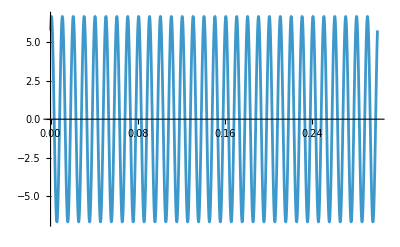

```mathematica
ClearAll["Global`*"];
suciastky={R1->10 *10^3,R2->10*10^3,R3->10*10^3,C2->10*10^-9,L->10*10^-3,Uz->3+6*ⅉ,ω->2*π*100};

rovnice={

0==Iz+Il+Ir1,
Ir1+Il==Ir2+Ir3,
Ir2==Ic2,

U1-U2==R1*Ir1,
U1-U2==L*Il*ⅉ*ω,
U2==R3*Ir3,
U2-U3==R2*Ir2,
Ic2==C2*U3*ⅉ*ω,
Uz==U1
};

nezname={Iz,Ir1,Ir2,Ir3,Ic2,Il,U1,U2,U3};
riesenie=Solve[rovnice/.suciastky,nezname][[1]]
Plot[Im[U3*ⅇ^(ⅉ*ω*t)]/.suciastky/.riesenie,{t,0,0.3}]
```